#### Create a sequence of directions

```mathematica
baharsFunction[x_] := 2x 
meryemsFunction[x_] := 

directions =Table[ , {50}]
```

{12,10,14,8,8,10,8,10,10,10,0,14,14,0,2,12,8,8,12,10,12,12,2,4,10,12,6,0,10,0,10,2,6,12,4,4,8,6,14,4,0,0,6,14,0,10,8,14,4,2}

#### Create rules that map direction numbers to direction vectors

```mathematica
rules = { 0 -> {1,1}, 1-> {1,-1}, 2-> {-1,1} , 3-> {-1,-1}, 4-> {0,1}, 5-> {1,0}, 6-> {0,-1}, 7-> {-1,0}}
```

{0→{1,1},1→{1,-1},2→{-1,1},3→{-1,-1},4→{0,1},5→{1,0},6→{0,-1},7→{-1,0}}

#### Create a table of direction vectors

```mathematica
table =directions/. rules
```

{12,10,14,8,8,10,8,10,10,10,{1,1},14,14,{1,1},{-1,1},12,8,8,12,10,12,12,{-1,1},{0,1},10,12,{0,-1},{1,1},10,{1,1},10,{-1,1},{0,-1},12,{0,1},{0,1},8,{0,-1},14,{0,1},{1,1},{1,1},{0,-1},14,{1,1},10,8,14,{0,1},{-1,1}}

#### Create sequence of coordinats

```mathematica
coordinates = Accumulate[table]
```

{12,22,36,44,52,62,70,80,90,100,{101,101},{115,115},{129,129},{130,130},{129,131},{141,143},{149,151},{157,159},{169,171},{179,181},{191,193},{203,205},{202,206},{202,207},{212,217},{224,229},{224,228},{225,229},{235,239},{236,240},{246,250},{245,251},{245,250},{257,262},{257,263},{257,264},{265,272},{265,271},{279,285},{279,286},{280,287},{281,288},{281,287},{295,301},{296,302},{306,312},{314,320},{328,334},{328,335},{327,336}}

#### Plot the coordinates

```mathematica
ListLinePlot[coordinates]
```

ListLinePlot::lpn: {12., 22., 36., 44., 52., 62., 70., 80., 90., 100., {101., 101.}, {115., 115.}, {129., 129.}, {130., 130.}, {129., 131.}, {141., 143.}, {149., 151.}, {157., 159.}, {169., 171.}, {179., 181.}, {191., 193.}, {203., 205.}, {202., 206.}, {202., 207.}, {212., 217.}, {224., 229.}, {224., 228.}, {225., 229.}, {235., 239.}, {236., 240.}, {246., 250.}, {245., 251.}, {245., 250.}, {257., 262.}, {257., 263.}, {257., 264.}, {265., 272.}, {265., 271.}, {279., 285.}, {279., 286.}, {280., 287.}, {281., 288.}, {281., 287.}, {295., 301.}, {296., 302.}, {306., 312.}, {314., 320.}, {328., 334.}, {328., 335.}, {327., 336.}} is not a list of numbers or pairs of numbers.

ListLinePlot[{12,22,36,44,52,62,70,80,90,100,{101,101},{115,115},{129,129},{130,130},{129,131},{141,143},{149,151},{157,159},{169,171},{179,181},{191,193},{203,205},{202,206},{202,207},{212,217},{224,229},{224,228},{225,229},{235,239},{236,240},{246,250},{245,251},{245,250},{257,262},{257,263},{257,264},{265,272},{265,271},{279,285},{279,286},{280,287},{281,288},{281,287},{295,301},{296,302},{306,312},{314,320},{328,334},{328,335},{327,336}}]

#### Animate the Plot

```mathematica
Animate[
  ListLinePlot[coordinates[[1;;i]], 
PlotRange->{{-10,10},{-10,10}}, 
AspectRatio->1, GridLines->Automatic],
{i, 1, 50,1}
]
```

```mathematica
points = {{0,0}, {1,0},{1,-2},{-2,-2}, {-2,2}, {3,2}, {3,-4}}
```

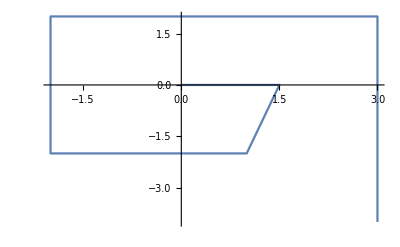

```mathematica
ListLinePlot[points]
```